## Exakt Solution

### Colors

```mathematica
{mmd,tu}={RGBColor[0.2,0.2,0.7],RGBColor[0.7,0.1,0.1]};
```

### Clear Parameter

```mathematica
Clear[A,ω,γ,fun,ifun]
```

### Exakt Solution

#### Jacobi-Elliptic Integral

```mathematica
ϕ=ArcSin[x/A];
m=-(A^2 γ)/(A^2 γ+2 ω0^2);
Simplify[m]
```

-(A^2 γ)/(2+A^2 γ)

```mathematica
ef=EllipticF[ϕ,m]
```

EllipticF[ArcSin[x/A],-(A^2 γ)/(2+A^2 γ)]

#### Pre-Factor

```mathematica
c=√2 A √(1/(A^4 γ+2 A^2 ω0^2))
```

√2 A √(1/(2 A^2+A^4 γ))

```mathematica
Simplify[c,A>0]
```

√2 √(1/(2+A^2 γ))

### Function t(x)

```mathematica
ftx[u_]:=c*ef/.x-> u
```

### Inverse Function x(t)

```mathematica
fxt[u_]:=A Sin[JacobiAmplitude[t/c,m]]/.t-> u
```

### ω(A)

```mathematica
fωA[u_]:=Pi/(2*ftx[A])/.A-> u
```

### A(ω)

```mathematica
fAω[u_]:=InverseFunction[fωA][u]
```

## Evaluation

### Parameter

```mathematica
{ω0,γ}={1,-0.1};
```

### Restoring Force

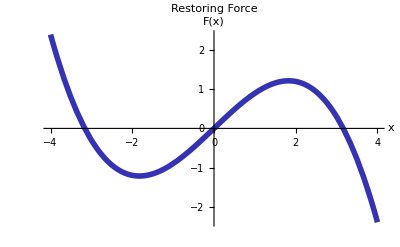

```mathematica
Fig1=Plot[ω0^2 x+γ x^3,{x,-4, 4},AxesLabel->{"x","F(x)"},PlotLabel->"Restoring Force",PlotStyle-> {mmd,Thickness-> 0.01}]
```

### ω over A

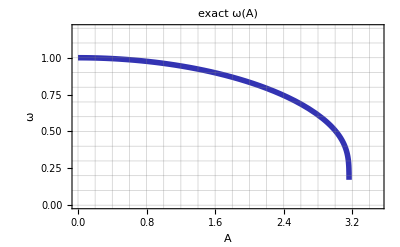

```mathematica
Fig2=Plot[fωA[A],{A,0, 4},FrameLabel->{A,ω},PlotLabel->"exact ω(A)",PlotStyle-> {mmd,Thickness-> 0.01},PlotRange-> {{0,3.5},{0,1.2}},Frame-> True,GridLines->{Range[0,3.5,0.2],Range[0,1.2,0.1]}]
```

### A over ω

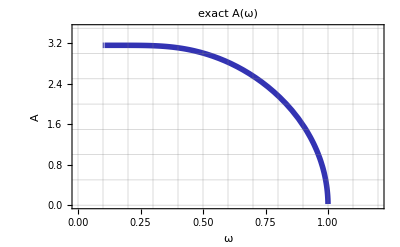

```mathematica
Clear[A,ω]
Fig3=Plot[fAω[ω],{ω,0, 1.2},FrameLabel->{ω,A},PlotLabel->"exact A(ω)",PlotStyle-> {mmd,Thickness-> 0.01},PlotRange-> {{0,1.2},{0,3.5}},GridLines->{Range[0,1.2,0.1],Range[0,3.5,0.5]},Frame-> True]
```

### Specify Frequency

```mathematica
ω=0.5;
T=2 π/ω;
A=fAω[ω]
```

3.00909

### x over t

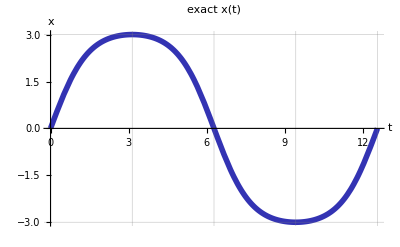

```mathematica
tend=T;
Fig4=Plot[fxt[t],{t,0, tend},AxesLabel->{t,x},PlotLabel->"exact x(t)",GridLines->{Range[0,tend,T/4],{-A,A}},PlotStyle-> {mmd,Thickness[0.01]}]
```

### Frequency content

```mathematica
n=15;
cosfun=Table[Cos[i ω t],{i,0,n}];
sinfun=Table[Sin[i ω t],{i,0,n}];
```

```mathematica
coscoeff=Chop[Quiet[2/T NIntegrate[# fxt[t],{t,0,T}]]]&/@cosfun;
sincoeff=Chop[Quiet[2/T NIntegrate[# fxt[t],{t,0,T}]]]&/@sinfun;
```

```mathematica
table1=Grid[Prepend[Table[{i,coscoeff⟦i+1⟧,sincoeff⟦i+1⟧},{i,0,n}],{"i","cos","sin"}],Frame->All]
```

i | cos | sin
0 | 0 | 0
1 | 0 | 3.29618
2 | 0 | 0
3 | 0 | 0.318066
4 | 0 | 0
5 | 0 | 0.0343234
6 | 0 | 0
7 | 0 | 0.00370851
8 | 0 | 0
9 | 0 | 0.000400696
10 | 0 | 0
11 | 0 | 0.0000432943
12 | 0 | 0
13 | 0 | 4.67785×10^-6
14 | 0 | 0
15 | 0 | 5.05431×10^-7

```mathematica
xf=cosfun.coscoeff+sinfun.sincoeff//Chop
```

3.29618 Sin[0.5 t]+0.318066 Sin[1.5 t]+0.0343234 Sin[2.5 t]+0.00370851 Sin[3.5 t]+0.000400696 Sin[4.5 t]+0.0000432943 Sin[5.5 t]+4.67785×10^-6 Sin[6.5 t]+5.05431×10^-7 Sin[7.5 t]

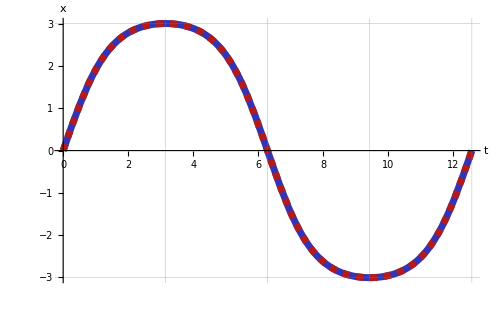

```mathematica
Fig5=Plot[{fxt[t],xf},{t,0, tend},AxesLabel->{t,x},GridLines->{Range[0,tend,T/4],{-A,A}},PlotStyle-> {{mmd,Thickness[0.01]},{tu,Dashed,Thickness[0.01]},{Orange,Thickness[0.003]}}, ImageSize->500]
```

## Perturbation Analysis

```mathematica
Clear[x,x0,x1,ϵ,δ,ω0,γ,f,f1,f2,g,ψ]
```

### DGL

```mathematica
dgl[x_]:=D[x,{t,2}]+ϵ δ D[x,t]+ω0^2 x+γ x^3-ϵ (f1 Cos[Ω t]+f2 Sin[Ω t])
```

### Ansatz

```mathematica
m=3;
eps=Table[ϵ^i,{i,0,m}];
func=Table[ToExpression[StringJoin["x",ToString[i],"[t]"]],{i,0,m}];
ans=func.eps
```

x0[t]+ϵ x1[t]+ϵ^2 x2[t]+ϵ^3 x3[t]

### Equations

```mathematica
eqst=Collect[Expand[dgl[ans]],ϵ];
eq0=eqst/.ϵ-> 0//Chop;
eqh=Coefficient[eqst,#]&/@Rest[eps];
```

```mathematica
Grid[Prepend[Partition[Riffle[eps,Prepend[eqh,eq0]],2],{"","DGL"}],Frame->All]
```

| DGL
1 | ω0^2 x0[t]+γ x0[t]^3+x0''[t]
ϵ | -f1 Cos[t Ω]-f2 Sin[t Ω]+ω0^2 x1[t]+3 γ x0[t]^2 x1[t]+δ x0'[t]+x1''[t]
ϵ^2 | 3 γ x0[t] x1[t]^2+ω0^2 x2[t]+3 γ x0[t]^2 x2[t]+δ x1'[t]+x2''[t]
ϵ^3 | γ x1[t]^3+6 γ x0[t] x1[t] x2[t]+ω0^2 x3[t]+3 γ x0[t]^2 x3[t]+δ x2'[t]+x3''[t]

### Parameter

```mathematica
ω0=1;
γ=-0.1;
d=0.022;
g=0.08;
eps=0.1;
δ=2*d*ω0/eps;
f=g/eps;
```

### Solve

#### 0-solution

```mathematica
x0[t]=Table[Cos[i Ω t],{i,0,n}].coscoeff+Table[Sin[i Ω t],{i,0,n}].sincoeff
```

3.29618 Sin[t Ω]+0.318066 Sin[3 t Ω]+0.0343234 Sin[5 t Ω]+0.00370851 Sin[7 t Ω]+0.000400696 Sin[9 t Ω]+0.0000432943 Sin[11 t Ω]+4.67785×10^-6 Sin[13 t Ω]+5.05431×10^-7 Sin[15 t Ω]

### 1-solution

```mathematica
Clear[ψ,f1,f2]
m1=15;
coeff1=Table[ToExpression[{StringJoin["A",ToString[i],"c"],StringJoin["A",ToString[i],"s"]}],{i,1,m1,2}]//Flatten;
Element[coeff1,Reals];
base1=Table[{Cos[i Ω t],Sin[i Ω t]},{i,1,m1,2}]//Flatten;
resbase=Table[{Cos[i Ω t],Sin[i Ω t]},{i,m1,3m1,2}]//Flatten;
x1[t]=base1.coeff1;
```

```mathematica
eqhb1=eqh⟦1⟧/.x0'[t]-> D[x0[t],t]/.x1''[t]-> D[x1[t],{t,2}]//TrigReduce;
eqhb1//MatrixForm;
eqs1=Coefficient[eqhb1,#]&/@base1/.Ω-> ω;
```

```mathematica
{f1,f2}=f Coefficient[TrigExpand[Cos[Ω t-ψ]],#]&/@{Cos[Ω t],Sin[Ω t]};
eqs1//MatrixForm;
```

```mathematica
sol1=Solve[Thread[eqs1==0],coeff1];
```

```mathematica
Clear[ψ]
res=Coefficient[eqhb1,#]&/@resbase/.Ω-> ω/.sol1⟦1⟧;
ressq=Total[res^2];
```

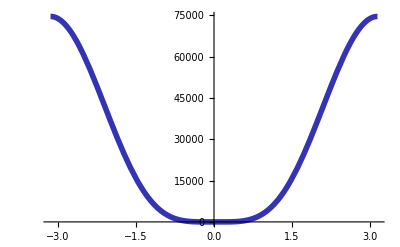

```mathematica
Fig6=Plot[ressq ,{ψ,-π,π},PlotRange-> {Automatic,Automatic},PlotStyle-> {mmd,Thickness-> 0.01}]
```

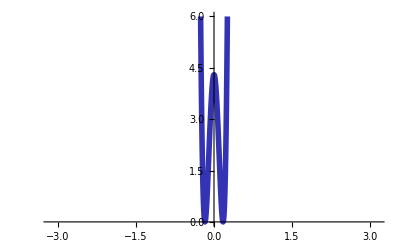

```mathematica
Fig7=Plot[ressq,{ψ,-π,π},PlotRange-> {Automatic,{0,6}},PlotStyle-> {mmd,Thickness-> 0.01}]
```

```mathematica
dres=D[ressq,ψ];
candidates={-1,1};
pos=ψ/.FindRoot[(dres)==0,{ψ,#}]&/@candidates
```

{-0.173845,0.173845}

```mathematica
tshift=pos/ω
```

{-0.347691,0.347691}

### Plot

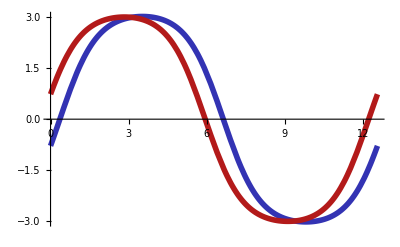

```mathematica
xp1s=(((x0[t]/.Ω-> ω)+(eps x1[t]/.sol1⟦1⟧/.Ω-> ω/.ψ->#))/.t-> (t+#/ω))&/@pos//Simplify;
Fig8=Plot[xp1s,{t,0,tend},PlotStyle-> {{mmd,Thickness-> 0.01},{tu,Thickness-> 0.01}}]
```

```mathematica
Maximize[#,t]&/@xp1s
```

{{3.01744,{t→3.53441}},{3.00132,{t→2.83903}}}

## Comparision with Numerical Integration

### Numerical Integration

#### Initial Condition

```mathematica
t0=Maximize[xp1s⟦1⟧,t]⟦2,1,2⟧;
y0s=Range[2,3,0.001];
Length[y0s]
dy0=0;
```

1001

```mathematica
t1=99 T;
t2=100T;
max=0;
maxindex=0;
```

#### Find solution

```mathematica
For[ i=1,i≤ Length[y0s],i++,
cury0=y0s⟦i⟧;
curnsol=Quiet[
Check[
NDSolve[{y''[t]+2*d*ω0*y'[t]+ω0^2*y[t]+γ*y[t]^3-g*Cos[Mod[ω t,T]]==0,y[t0]==cury0,y'[t0]==dy0},y,{t,0,t2}],
"failed"]
];
If[curnsol== "failed",Continue[]];
curmax=Max[(y[#]/.curnsol⟦1⟧)&/@Range[t1,t2,T/99]];
If[curmax>max,
max=curmax;
maxindex=i;
];
If[max>2,Break[]];
];
Print[ToString[max]];
Print[ToString[maxindex]];
```

3.01606

955

### Find solution with no transients

#### continuation

```mathematica
t3=500 T;
{y0,dy0}={y[0],y'[0]}/.curnsol⟦1⟧;
nsol1=NDSolve[{y''[t]+2*d*ω0*y'[t]+ω0^2*y[t]+γ*y[t]^3-g*Cos[Mod[ω t,T]]==0,y[0]==y0,y'[0]==dy0},y,{t,0,t3},PrecisionGoal->25];
```

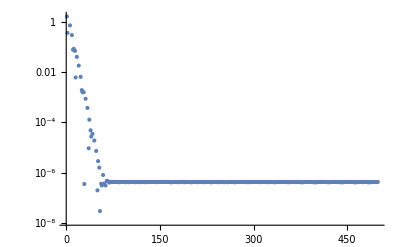

```mathematica
Fig9=ListLogPlot[Differences[y[#]/.nsol1⟦1⟧&/@Range[0,t3,T]],Joined-> False]
```

#### Initial Conditions and Solution

```mathematica
{y0,dy0}={y[t3],y'[t3]}/.nsol1⟦1⟧;
nsol2=NDSolve[{y''[t]+2*d*ω0*y'[t]+ω0^2*y[t]+γ*y[t]^3-g*Cos[Mod[ω t,T]]==0,y[0]==y0,y'[0]==dy0},y,{t,0,T}];
```

#### Plot

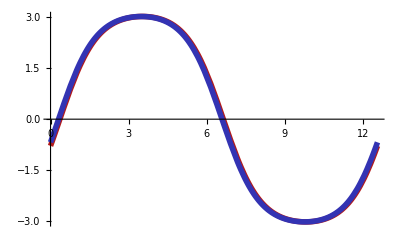

```mathematica
numint=Plot[y[t]/.nsol2,{t,0,T},PlotStyle-> {mmd,Thickness-> 0.01}];
Fig10=Show[Plot[xp1s⟦1⟧,{t,0,T},PlotStyle-> {tu,Thickness-> 0.01}],numint]
```

```mathematica
Grid[{{"x0","dx0"},{y0,dy0}},Frame->All]
```

x0 | dx0
-0.679357 | 2.13541

## Comparision with Harmonic Balance

### Ansatz

```mathematica
r=5;
HBcoeff=Table[ToExpression[{StringJoin["HB",ToString[i],"c"],StringJoin["HB",ToString[i],"s"]}],{i,1,r,2}]//Flatten;
HBbase=Table[{Cos[i Ω t],Sin[i Ω t]},{i,1,r,2}]//Flatten;
HBans=HBbase.HBcoeff;
```

### Equations

```mathematica
HBres=D[HBans,{t,2}]+2*d*ω0*D[HBans,t]+ω0^2*HBans+γ*HBans^3-g*Cos[Ω t]//TrigReduce;
HBeqs=Coefficient[HBres,#]&/@HBbase/.Ω-> ω;
```

### Solutions

```mathematica
HBSol=DeleteCases[HBcoeff/.Solve[Thread[HBeqs==0],HBcoeff],x_/;!x∈Reals];
{HBx1,HBx2,HBx3}=((HBbase/.Ω-> ω).#)&/@HBSol
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.106696 Cos[0.5 t]-0.0000242422 Cos[1.5 t]+3.93477×10^-9 Cos[2.5 t]+0.00313333 Sin[0.5 t]-8.58433×10^-7 Sin[1.5 t]+2.8847×10^-10 Sin[2.5 t],0.639989 Cos[0.5 t]+0.181402 Cos[1.5 t]+0.0285461 Cos[2.5 t]+3.22219 Sin[0.5 t]+0.258343 Sin[1.5 t]+0.0176217 Sin[2.5 t],-0.520335 Cos[0.5 t]-0.139012 Cos[1.5 t]-0.0234053 Cos[2.5 t]+3.26334 Sin[0.5 t]+0.287398 Sin[1.5 t]+0.0249548 Sin[2.5 t]}

### Stability

```mathematica
stabdgls=(ω0^2+3 (#)^2 γ) Δx[t]+2*d*ω0* Δx'[t]+Δx''[t]&/@{HBx1,HBx2,HBx3};curAs=Table[{Δx[T/2],Δx'[T/2]}/.NDSolve[Join[{#==0},Thread[{Δx[0],Δx'[0]}==UnitVector[2,k]]],{Δx,Δx'},{t,0,T/2}]⟦1⟧,{k,1,2}]&/@stabdgls;
stabs=If[1≥ Max[Abs[Eigenvalues[#]]],"stable","instable"]&/@curAs
```

{stable,instable,stable}

### Matching HB -> PA

```mathematica
xp1sref=xp1s/.t-> 1
```

{1.33999,2.3053}

```mathematica
HBx2ref=HBx2/.t-> 1;
indHBx2=Position[xp1sref,Nearest[xp1sref,HBx2ref]⟦1⟧]⟦1,1⟧;
```

```mathematica
HBx3ref=HBx3/.t-> 1;
indHBx3=Position[xp1sref,Nearest[xp1sref,HBx3ref]⟦1⟧]⟦1,1⟧;
```

### Plot

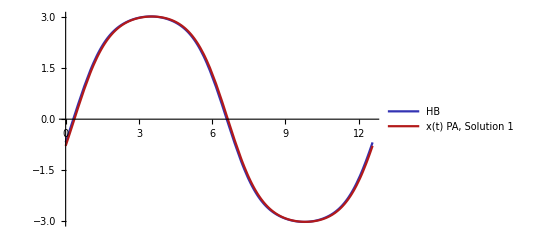

```mathematica
Fig11=Plot[{HBx3,xp1s⟦indHBx3⟧},{t,0,T},PlotStyle-> {mmd,tu}, PlotLegends->{"HB", StringJoin["x(t) PA, Solution ",ToString[ indHBx3]] }]
```

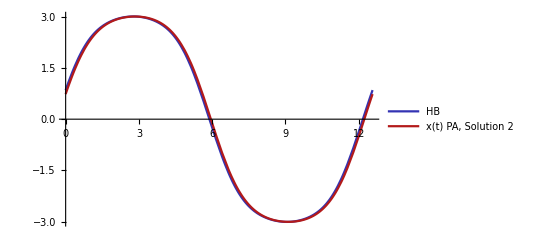

```mathematica
Fig12=Plot[{HBx2,xp1s⟦indHBx2⟧},{t,0,T},PlotStyle-> {mmd,tu}, PlotLegends->{"HB", StringJoin["x(t) PA, Solution ",ToString[ indHBx2]] }]
```